```mathematica
hahahah

hahha
```

hahahah

hahha

```mathematica
cuscus = 1
```

1

```mathematica
1 =? pi
```

Set::setraw: Cannot assign to raw object 1.

Missing[UnknownSymbol,pi]

```mathematica
tudum = {show1, movie1, docs} (* comment*)
```

{show1,movie1,docs}

```mathematica
/pi
```

```mathematica
1/2
```

1/2

```mathematica
Pi + Alphabet
```

Alphabet+π

```mathematica
tudum[2]
```

{show1,movie1,docs}[2]

```mathematica
(*kdyz je promenna modra tak jeste nema hodnotu, pokud je cerna tak uz to je nova promenna*)
```

```mathematica
a = {1, 2, 3, 4, -10, 1000000000000000000}
```

{1,2,3,4,-10,1000000000000000000}

```mathematica
b= {4/3, -2.3, √5}
```

{4/3,-2.3,√5}

```mathematica
Pi//N  (*prevedu na nepresne cislo*)
```

3.14159

```mathematica
N[π] (*ESC + p + ESC -> bude alpha *)
```

3.14159

```mathematica
(*funkce maji hranaty zavorky*)
```

```mathematica
N@π
```

3.14159

```mathematica
c1 =2*Pi
```

2 π

```mathematica
c2 =2.*Pi (*opet prevedene na nepresne cislo*)
```

6.28319

```mathematica
cc= {ⅇ, π/6}; (*strednik na potlaceni outputu*)
```

```mathematica
(* 3 typy rovnase -> = (prirazeni), == (rovnice) := (definice vlastnich fci)*)
```

```mathematica
promenna = "nema_podrazitka" (* podrzitko se pouziva pro definici funkci*)
```

nema_podrazitka

```mathematica
(*mezi cislem a pismenem se predpoklada nasobeni!!*)
```

```mathematica
x = 10
y=25
z=8
```

10

25

8

```mathematica
r= x^2 +5y -6z
```

177

```mathematica
225-48
```

177

```mathematica
(*predpocitat cely notebook: Evaluation -> EvaluateNotebook*)
```

```mathematica
ClearAll["Global`*"](*pocitat funkci s cistym stitem; do dokumentace se da dostat pred F1*)
x=7; y=5;z=3
```

3

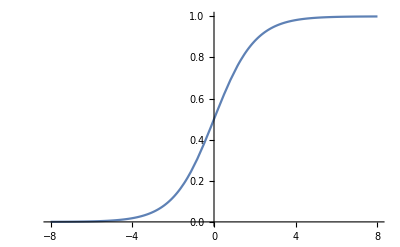

```mathematica
(*funkce vestavene vs definovane uzivatele*)
?Sin
?ClearAll
?Plot

sigmoida[x_,γ_]:=1/(1+ⅇ^(-x*γ)) (*ESC ee ESC = ⅇ*)
Plot[sigmoida[a,1], {a,-8,8}]
```

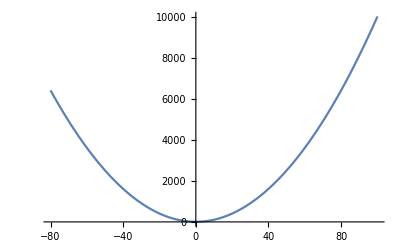

```mathematica
func[x_, y_, z_] := x+2y-z
Plot[func[x,4,2],{x, 100, -80}]
```

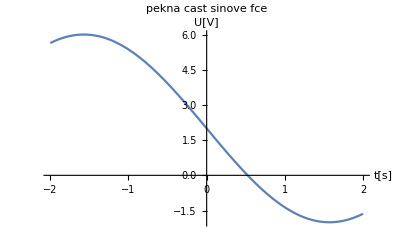

```mathematica
func2[a_, b_, c_] := b*Sin[a-Pi] + c
Plot[func2[a, 4, 2], {a, 2,-2}, PlotLabel->"pekna cast sinove fce", AxesLabel-> {"t[s]", "U[V]"}]
(*funkce s peknyma popiskama*)
(* -> je "dosad to kdyz je to potreba" *)
```